```mathematica
probabilityNormalDistributionBetween[mean_,stdev_,a_,b_,numberOfStdevToShow_:4]:=Module[{plot1,plot2},
plot1=Plot[PDF[NormalDistribution[mean,stdev],x],{x,mean-stdev*numberOfStdevToShow,mean+stdev*numberOfStdevToShow},AxesLabel->{"Random Variable (standard deviation)", "Probability X=x"}];
plot2=Plot[PDF[NormalDistribution[mean,stdev],x],{x,a,b},Filling->Axis,PlotRange->PlotRange[plot1]];
Print[Show[plot1,plot2]];
Return[NProbability[a<x<b,x\[Distributed]NormalDistribution[mean,stdev]]];
];
probabilityNormalDistributionGreaterThan[mean_,stdev_,a_,numberOfStdevToShow_:4]:=Module[{plot1,plot2},
plot1=Plot[PDF[NormalDistribution[mean,stdev],x],{x,mean-stdev*numberOfStdevToShow,mean+stdev*numberOfStdevToShow},AxesLabel->{"Random Variable (standard deviation)", "Probability X=x"}];
plot2=Plot[PDF[NormalDistribution[mean,stdev],x],{x,a,mean+stdev*numberOfStdevToShow},Filling->Axis,PlotRange->PlotRange[plot1]];
Print[Show[plot1,plot2]];
Return[NProbability[a<x,x\[Distributed]NormalDistribution[mean,stdev]]];
];
probabilityNormalDistributionLessThan[mean_,stdev_,a_,numberOfStdevToShow_:4]:=Module[{plot1,plot2},
plot1=Plot[PDF[NormalDistribution[mean,stdev],x],{x,mean-stdev*numberOfStdevToShow,mean+stdev*numberOfStdevToShow},AxesLabel->{"Random Variable (standard deviation)", "Probability X=x"}];
plot2=Plot[PDF[NormalDistribution[mean,stdev],x],{x,mean-stdev*numberOfStdevToShow,a},Filling->Axis,PlotRange->PlotRange[plot1]];
Print[Show[plot1,plot2]];
Return[NProbability[x<a,x\[Distributed]NormalDistribution[mean,stdev]]];
];
plotNormalDistributionBetween[mean_,stdev_,a_,b_,numberOfStdevToShow_:4]:=Module[{plot1,plot2},
plot1=Plot[PDF[NormalDistribution[mean,stdev],x],{x,mean-stdev*numberOfStdevToShow,mean+stdev*numberOfStdevToShow},AxesLabel->{"Random Variable (standard deviation)", "Probability X=x"}];
plot2=Plot[PDF[NormalDistribution[mean,stdev],x],{x,a,b},Filling->Axis,PlotRange->PlotRange[plot1]];
Return[Show[plot1,plot2]];
];
plotNormalDistributionGreaterThan[mean_,stdev_,a_,numberOfStdevToShow_:4]:=Module[{plot1,plot2},
plot1=Plot[PDF[NormalDistribution[mean,stdev],x],{x,mean-stdev*numberOfStdevToShow,mean+stdev*numberOfStdevToShow},AxesLabel->{"Random Variable (standard deviation)", "Probability X=x"}];
plot2=Plot[PDF[NormalDistribution[mean,stdev],x],{x,a,mean+stdev*numberOfStdevToShow},Filling->Axis,PlotRange->PlotRange[plot1]];
Return[Show[plot1,plot2]];
];
plotNormalDistributionLessThanPlot[mean_,stdev_,a_,numberOfStdevToShow_:4]:=Module[{plot1,plot2},
plot1=Plot[PDF[NormalDistribution[mean,stdev],x],{x,mean-stdev*numberOfStdevToShow,mean+stdev*numberOfStdevToShow},AxesLabel->{"Random Variable (standard deviation)", "Probability X=x"}];
plot2=Plot[PDF[NormalDistribution[mean,stdev],x],{x,mean-stdev*numberOfStdevToShow,a},Filling->Axis,PlotRange->PlotRange[plot1]];
Return[Show[plot1,plot2]];
];
```

```mathematica
nPr[n_,r_]:=Factorial[n]/Factorial[n-r]
nCr[n_,r_]:=Binomial[n,r]
pascalsTraingle[rows_]:=Column[Table[Binomial[n,r],{n,0,rows-1},{r,0,n}],Center]
```

```mathematica
probabilityAGivenB[aAndB_,b_]:=aAndB/b
```

```mathematica
standardDeviationFromVariance[variance_]:=√variance
varianceFromStandardDeviation[stdev_]:=stdev^2
```

```mathematica
expectedBinomial[n_,p_]:=n*p
varianceBinomial[n_,p_]:=n*p*(1-p)
```

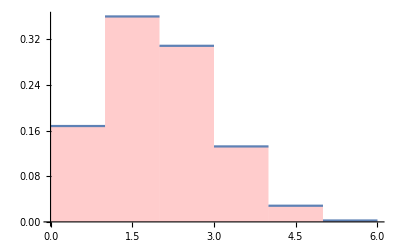

```mathematica
DiscretePlot[PDF[BinomialDistribution[5,0.3],x],{x,0,5},ExtentSize->Right,Filling->Axis,FillingStyle->Red]
```

```mathematica
ClearAll[plotBinomialDistributionBetween]
```

```mathematica
plotBinomialDistributionBetweenInclusive[n_,p_,a_Integer,b_Integer]:=Module[{i,plot1,plots},
plot1=DiscretePlot[PDF[BinomialDistribution[n,p],x],{x,0,n},ExtentSize->Right,Filling->Axis,FillingStyle->Red];
plots={};
For[i=a,i≤b,i++,
AppendTo[plots,DiscretePlot[PDF[BinomialDistribution[n,p],x],{x,i,i},ExtentSize->Right,Filling->Axis,FillingStyle->Blue]];
];
Return[Show[plot1,plots]];
];
plotBinomialDistributionBetweenExclusive[n_,p_,a_Integer,b_Integer]:=Module[{i,plot1,plots},
plot1=DiscretePlot[PDF[BinomialDistribution[n,p],x],{x,0,n},ExtentSize->Right,Filling->Axis,FillingStyle->Red];
plots={};
For[i=a+1,i≤b-1,i++,
AppendTo[plots,DiscretePlot[PDF[BinomialDistribution[n,p],x],{x,i,i},ExtentSize->Right,Filling->Axis,FillingStyle->Blue]];
];
Return[Show[plot1,plots]];
];
plotBinomialDistributionGreaterThan[n_,p_,a_Integer]:=Module[{i,plot1,plots},
plot1=DiscretePlot[PDF[BinomialDistribution[n,p],x],{x,0,n},ExtentSize->Right,Filling->Axis,FillingStyle->Red];
plots={};
For[i=a+1,i≤n,i++,
AppendTo[plots,DiscretePlot[PDF[BinomialDistribution[n,p],x],{x,i,i},ExtentSize->Right,Filling->Axis,FillingStyle->Blue]];
];
Return[Show[plot1,plots]];
];
plotBinomialDistributionLessThan[n_,p_,a_Integer]:=Module[{i,plot1,plots},
plot1=DiscretePlot[PDF[BinomialDistribution[n,p],x],{x,0,n},ExtentSize->Right,Filling->Axis,FillingStyle->Red];
plots={};
For[i=0,i≤a-1,i++,
AppendTo[plots,DiscretePlot[PDF[BinomialDistribution[n,p],x],{x,i,i},ExtentSize->Right,Filling->Axis,FillingStyle->Blue]];
];
Return[Show[plot1,plots]];
];
plotBinomialDistributionEquals[n_,p_,a_Integer]:=Module[{i,plot1,plots},
plot1=DiscretePlot[PDF[BinomialDistribution[n,p],x],{x,0,n},ExtentSize->Right,Filling->Axis,FillingStyle->Red];
plots=DiscretePlot[PDF[BinomialDistribution[n,p],x],{x,a,a},ExtentSize->Right,Filling->Axis,FillingStyle->Blue];
Return[Show[plot1,plots]];
];
probabilityBinomialDistributionBetweenInclusive[n_,p_,a_Integer,b_Integer]:=Module[{i,plot1,plots},
plot1=DiscretePlot[PDF[BinomialDistribution[n,p],x],{x,0,n},ExtentSize->Right,Filling->Axis,FillingStyle->Red];
plots={};
For[i=a,i≤b,i++,
AppendTo[plots,DiscretePlot[PDF[BinomialDistribution[n,p],x],{x,i,i},ExtentSize->Right,Filling->Axis,FillingStyle->Blue]];
];
Print[Show[plot1,plots]];
Return[Probability[a≤x≤b,x\[Distributed]BinomialDistribution[5,0.3]]];
];
probabilityBinomialDistributionBetweenExclusive[n_,p_,a_Integer,b_Integer]:=Module[{i,plot1,plots},
plot1=DiscretePlot[PDF[BinomialDistribution[n,p],x],{x,0,n},ExtentSize->Right,Filling->Axis,FillingStyle->Red];
plots={};
For[i=a+1,i≤b-1,i++,
AppendTo[plots,DiscretePlot[PDF[BinomialDistribution[n,p],x],{x,i,i},ExtentSize->Right,Filling->Axis,FillingStyle->Blue]];
];
Print[Show[plot1,plots]];
Return[Probability[a<x<b,x\[Distributed]BinomialDistribution[5,0.3]]];
];
probabilityBinomialDistributionGreaterThan[n_,p_,a_Integer]:=Module[{i,plot1,plots},
plot1=DiscretePlot[PDF[BinomialDistribution[n,p],x],{x,0,n},ExtentSize->Right,Filling->Axis,FillingStyle->Red];
plots={};
For[i=a+1,i≤n,i++,
AppendTo[plots,DiscretePlot[PDF[BinomialDistribution[n,p],x],{x,i,i},ExtentSize->Right,Filling->Axis,FillingStyle->Blue]];
];
Print[Show[plot1,plots]];
Return[Probability[x>a,x\[Distributed]BinomialDistribution[5,0.3]]];
];
probabilityBinomialDistributionLessThan[n_,p_,a_Integer]:=Module[{i,plot1,plots},
plot1=DiscretePlot[PDF[BinomialDistribution[n,p],x],{x,0,n},ExtentSize->Right,Filling->Axis,FillingStyle->Red];
plots={};
For[i=0,i≤a-1,i++,
AppendTo[plots,DiscretePlot[PDF[BinomialDistribution[n,p],x],{x,i,i},ExtentSize->Right,Filling->Axis,FillingStyle->Blue]];
];
Print[Show[plot1,plots]];
Return[Probability[x<a,x\[Distributed]BinomialDistribution[5,0.3]]];
];
probabilityBinomialDistributionEquals[n_,p_,a_Integer]:=Module[{i,plot1,plots},
plot1=DiscretePlot[PDF[BinomialDistribution[n,p],x],{x,0,n},ExtentSize->Right,Filling->Axis,FillingStyle->Red];
plots=DiscretePlot[PDF[BinomialDistribution[n,p],x],{x,a,a},ExtentSize->Right,Filling->Axis,FillingStyle->Blue];
Print[Show[plot1,plots]];
Return[Probability[x==a,x\[Distributed]BinomialDistribution[5,0.3]]];
];
```

```mathematica
Probability[x>1,x\[Distributed]BinomialDistribution[5,0.3]]+Probability[x<1,x\[Distributed]BinomialDistribution[5,0.3]]+Probability[x==1,x\[Distributed]BinomialDistribution[5,0.3]]
```

1.

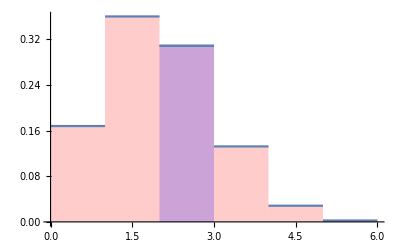

```mathematica
plotBinomialDistributionBetweenExclusive[5,0.3,1,3]
```